A Theory of Dark Matter--N. Arkani-Hamed, D. Finkbeiner, T. Slatyer, N. Weiner

Assumptions: 
•  Dark Matter are WIMPs.

Issues:
•  There exist cosmic rays with energies that are unexpectedly above thermal spectrum.   What is expected thermal spectra?
•  If decay of WIMPs to leptons contribute to this unexpected cosmic ray spectra then their mass M_X∈[500 Gev,800Gev].
•  Limits on p and π^0-γ constrain hadronic channels of dark matter.  What are these limits and what are the hadronic channels?

Conclusions:
•  A new long-range force may explain these observations.  
•  This new force allows Somerfeld enhancement without altering weak-scale annihilation cross section during dark matter freeze-out.
•  If DM⟶ϕ[force carrier, low mass]⟶leptons⟹no hadronic modes
•  If DM⟶ϕ[force carrier, non-Abelian gauge bosons]⟹DM[multiplet of states] ⟹eXciting dark matter

```mathematica
<<Local`QFTToolKit`
<<PhysicalConstants`
<<Units`
DeclareIndexFlavor[{dotted,Orange}]
DeclareIndexFlavor[{undotted,Blue}]
Clear[tu,td]
DefineTensorShortcuts[{{η,v,D,F,Λ,H,R,τ,μ,u,Y,Γ,Q,d,L,Z,W,λ,T,t,M,ν,S,C,U,m,δ},1},
{{m,G,b,u,H,Q,e,ν,ϕ,ψ,a},2},
{{σ,ξ,y,a,u,Q,y,M,S,T},3},
{{V,ϕ},4},
{{V},5}
]
AddBaseIndex[{dotted,{1,2}}];
AddBaseIndex[{undotted,{1,2}}];
Put[SaveFile=NBname["stub"]<>".out"]
```

```mathematica
PR1["Weak-scale thermal particle abundance, Ω, is given by: ",
tmp=Ω h^2->.1 ("<σv>_freeze"/(3 10^-26 units[cm^3 s^-1]))^-1
]
```

Weak-scale thermal particle abundance, Ω, is given by: h^2 Ω→(3.×10^-27 units[cm^3/s])/(<σv>_freeze)

```mathematica
PR1["Sommerfeld enhancement to increase cross section--classical picture.
With no long-range forces the physical cross-section is: ",
σd[0]->π R^2," With long-range attractive for the cross-section becomes: ",
σ->σd[0](1+vd[esc]^2/v^2)," where ",vd[esc]^2->2 Gd[N] M/R," is the escape velocity from the surface. For ",v≪vd[esc]," there is large enhancement of the cross-section."
]
```

Sommerfeld enhancement to increase cross section--classical picture.
With no long-range forces the physical cross-section is: σ_0^0→π R^2 With long-range attractive for the cross-section becomes: σ→(1+((v_esc^esc)^2)/v^2) σ_0^0 where (v_esc^esc)^2→(2 M G_N^N)/R is the escape velocity from the surface. For v≪v_esc^esc there is large enhancement of the cross-section.

```mathematica
PR1["Sommerfeld enhancement--quantum picture.
Arises when a particle's Compton wavelength ",λd[Compton]>(α Md[DM])^-1," i.e., when DM bound states are present and ",10^-3≲α≲10^-1," as in the standard model.",CR[" The particle referenced is the DM particle? The bound state is required for annihilation."]," Assume Yukawa interaction, i.e., the product Lagrangian terms, of DM χ, a mediator particle ϕ, and coupling strength λ: ",Subscript[ℒ, yukawa]->λ.ϕ.χ
]
```

Sommerfeld enhancement--quantum picture.
Arises when a particle's Compton wavelength λ_Compton^Compton>1/(α M_DM^DM) i.e., when DM bound states are present and 1/1000≲α≲1/10 as in the standard model. The particle referenced is the DM particle? The bound state is required for annihilation. Assume Yukawa interaction, i.e., the product Lagrangian terms, of DM χ, a mediator particle ϕ, and coupling strength λ: ℒ_yukawa→λ.ϕ.χ

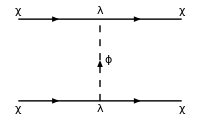
The radial two-body non-relativistic Schrodinger equation for the s-wave wavefunction is: Ψ[r]→ψ[r]/r ⇒ -V[r] ψ[r]+ψ''[r]/m_χ^χ==-v^2 m_χ^χ ψ[r] where v is the CM velocity of χ and V[r]→-(ⅇ^(-r m_ϕ^ϕ) λ^2)/(4 π r)
The interaction diagram:-Graphics-

```mathematica
PR1["The radial two-body non-relativistic Schrodinger equation for the s-wave wavefunction is: ",Ψ[r]->ψ[r]/r,imply,e3=D[ψ[r],{r,2}]/md[χ]-V[r]ψ[r]==-md[χ] v^2 ψ[r]," where v is the CM velocity of χ",and,V[r]->-λ^2/(4π r)Exp[-md[ϕ]r],
NL,"The interaction diagram:",
Graphics[{{MidArrow[{{0,0},{1,0}}],MidArrow[{{1,0},{2,0}}],MidArrow[{{0,1},{1,1}}],MidArrow[{{1,1},{2,1}}],Dashed,MidArrow[{{1,0},{1,1}}]},
Inset[λ,{1,-.1}],Inset[λ,{1,1.1}],Inset[χ,{0,-.1}],Inset[χ,{0,1.1}],Inset[χ,{2,-.1}],Inset[χ,{2,1.1}],Inset[ϕ,{1.1,.5}]},
ImageSize->200],
""
]
```

```mathematica
PR1["Appendix A: Sommerfeld enhancement reviewed.",NL,
"Annihilation potential: ",
Hd[ann]->Ud[ann]DiracDelta[space@r],
"Assume plane+partial wave asymptotic solution ",
ψ[r]->Exp[I k z]+f[θ] Exp[I k r]/r
," to the Schrodinger equation: ",
eA2=-1/(2M)∇∇ψd[k]+V[r]ψd[k]==k^2/(2M)ψd[k],
"The annihilation potential alters the cross-section at the origin, ",
σ->σd[0]Sd[k]," where ",Sd[k]->Abs[ψd[x][0]]^2
]
```

Appendix A: Sommerfeld enhancement reviewed.
Annihilation potential: H_ann^ann→DiracDelta[r] U_ann^annAssume plane+partial wave asymptotic solution ψ[r]→ⅇ^(ⅈ k z)+(ⅇ^(ⅈ k r) f[θ])/r to the Schrodinger equation: -(∇∇ψ_k^k)/(2 M)+ψ_k^k V[r]==(k^2 ψ_k^k)/(2 M)The annihilation potential alters the cross-section at the origin, σ→S_k^k σ_0^0 where S_k^k→Abs[ψ_x^x[0]]^2

```mathematica
PR1["Radial part of Schrodinger equation: ",eA7=-1/(2 M)1/r^2 D[r^2 D[Rdd[k,l][r],r],r]+(l(l+1)/r^2+V[r])Rdd[k,l][r]==k^2/(2 M)Rdd[k,l][r]," with ",sub=V[r]->0," the solution is, ",
tmp=DSolve[(eA7/.sub),Rdd[k,l][r],r][[1,1]],CR[" Need to show asymptotic solution A8 satisfies and "],{Rdd[k,l][0]->0,{l≠0}},
ExtractPattern[tmp,SphericalBesselJ[a_,b_]][[1]]
]
```

Radial part of Schrodinger equation: ((l (1+l))/r^2+V[r]) R_kl^kl[r]-(2 r (R_kl^kl)'[r]+r^2 (R_kl^kl)''[r])/(2 M r^2)==(k^2 R_kl^kl[r])/(2 M) with V[r]→0 the solution is, R_kl^kl[r]→C[1] SphericalBesselJ[1/2 (-1+√(1+8 l M+8 l^2 M)),k r]+C[2] SphericalBesselY[1/2 (-1+√(1+8 l M+8 l^2 M)),k r] Need to show asymptotic solution A8 satisfies and {R_kl^kl[0]→0,{l≠0}}SphericalBesselJ[1/2 (-1+√(1+8 l M+8 l^2 M)),k r]

```mathematica
PR1["Determine ",ψd[k][0]," to compute Sommerfeld factor.
As ",r->∞," normalize to",imply,eA8=Rdd[k_,l_]->1/r Sin[k r-1/2 l π+δ[r]]," and expanding ",
eA10=ψd[k_][r_,θ_]->1/k Sum[I^l(2 l+1)Exp[I δd[l]]LegendreP[l,Cos[θ]]Rdd[k,l][r],l],NL,"Then, ",tmp=ψd[k][0,θ],yield,tmp=tmp/.eA10,yield,tmp=tmp/.l->0/.Sum[a_,b_]->a,back,
CR["The assumption that Rdd[k,l]->r^l if the V[r] term can be ignored needs checking. "]
]
```

Determine ψ_k^k[0] to compute Sommerfeld factor.
As r→∞ normalize to ⇒ R_k_l_^k_l_→-Sin[(l π)/2-k r-δ[r]]/r and expanding ψ_k_^k_[r_,θ_]→(∑_l ⅈ^l ⅇ^(ⅈ δ_l^l) (1+2 l) LegendreP[l,Cos[θ]] R_kl^kl[r])/k
Then, ψ_k^k[0,θ] ⟶ (∑_l ⅈ^l ⅇ^(ⅈ δ_l^l) (1+2 l) LegendreP[l,Cos[θ]] R_kl^kl[0])/k ⟶ (ⅇ^(ⅈ δ_0^0) R_k0^k0[0])/k ⟵The assumption that Rdd[k,l]->r^l if the V[r] term can be ignored needs checking.

```mathematica
tmp=eA7;
tmp=Map[# r^2&,tmp]//Expand
tmp=Solve[tmp,Rdd[k,l][r]][[1,1]]
Map[Series[#,{r,0,2}]&,tmp]//Normal
CR["check if RHS is correct."]
```

l R_kl^kl[r]+l^2 R_kl^kl[r]+r^2 V[r] R_kl^kl[r]-(r (R_kl^kl)'[r])/M-(r^2 (R_kl^kl)''[r])/(2 M)==(k^2 r^2 R_kl^kl[r])/(2 M)

R_kl^kl[r]→(2 r (R_kl^kl)'[r]+r^2 (R_kl^kl)''[r])/(2 l M+2 l^2 M-k^2 r^2+2 M r^2 V[r])

R_kl^kl[0]+r (R_kl^kl)'[0]+1/2 r^2 (R_kl^kl)''[0]→(r (R_kl^kl)'[0])/((l+l^2) M)+(3 r^2 (R_kl^kl)''[0])/(2 (l+l^2) M)

check if RHS is correct.

```mathematica
PR1[" Using ",{sub=Rdd[k,0][r]->χd[k][r]/r,sub1=Map[D[#,r]&,sub],
sub2=Map[D[#,{r,2}]&,sub]}//Column,
" the radial part of the Schrodinger equation ",eA7,yield,"A12",yield,eA12=eA7/.l->0/.{sub,sub1,sub2}//Simplify
]
```

Using R_k0^k0[r]→χ_k^k[r]/r
(R_k0^k0)'[r]→-χ_k^k[r]/r^2+((χ_k^k)'[r])/r
(R_k0^k0)''[r]→(2 χ_k^k[r])/r^3-(2 (χ_k^k)'[r])/r^2+((χ_k^k)''[r])/r the radial part of the Schrodinger equation ((l (1+l))/r^2+V[r]) R_kl^kl[r]-(2 r (R_kl^kl)'[r]+r^2 (R_kl^kl)''[r])/(2 M r^2)==(k^2 R_kl^kl[r])/(2 M) ⟶ A12 ⟶ ((k^2-2 M V[r]) χ_k^k[r]+(χ_k^k)''[r])/(M r)==0

```mathematica
PR1["For ",sub=V[r]->0,", A12: ",eA12,", has solution ",Yield,
tmp=DSolve[(eA12/.V[r]->0),χd[k][r],r][[1]],CR[" There is no generalized solution for V[r]≠0. Find a conservative radial plane wave solution and assume the finite range potential only affects the phase of radial wave."]
];
```

For V[r]→0, A12: ((k^2-2 M V[r]) χ_k^k[r]+(χ_k^k)''[r])/(M r)==0, has solution 
→ {χ_k^k[r]→C[1] Cos[k r]+C[2] Sin[k r]} There is no generalized solution for V[r]≠0. Find a conservative radial plane wave solution and assume the finite range potential only affects the phase of radial wave.

```mathematica
PR1["Normalization condition at ∞: ",eA13=χd[k_][r_]->Sin[k r+δ],
NL,"Condition at r->0: ",eA14=χd[k_][r_]->r D[χd[k][r],r]
]
```

Normalization condition at ∞: χ_k_^k_[r_]→Sin[k r+δ]
Condition at r->0: χ_k_^k_[r_]→r (χ_k^k)'[r]

```mathematica
PR1["The potential ",eA19=V[r_]->-α/(2 r)," and A12",yield,
tmp=eA12/.eA19,yield,
tmp=Map[# M r&,tmp]//Expand,
NL,"The general solution ",yield,
tmpχ=DSolve[tmp,χd[k][r],r][[1,1]]
]
```

The potential V[r_]→-α/(2 r) and A12 ⟶ ((k^2+(M α)/r) χ_k^k[r]+(χ_k^k)''[r])/(M r)==0 ⟶ k^2 χ_k^k[r]+(M α χ_k^k[r])/r+(χ_k^k)''[r]==0
The general solution  ⟶ χ_k^k[r]→ⅇ^(-√(k^2) r+(-√(-k^2)+√(k^2)) r) r C[2] Hypergeometric1F1[1+(-4 √(k^2)-2 (-2 √(k^2)+M α))/(4 √(-k^2)),2,2 √(-k^2) r]+ⅇ^(-√(k^2) r+(-√(-k^2)+√(k^2)) r) r C[1] HypergeometricU[1+(-4 √(k^2)-2 (-2 √(k^2)+M α))/(4 √(-k^2)),2,2 √(-k^2) r]

```mathematica
PR1["The solution in the limit ",sub=r->0,yield,
Limit[tmpχ[[2]],r->0],imply,sub=C[1]->0," from BC.\nThen ",
tmp=tmpχ/.sub//PowerExpand,Yield,
tmp1=ExtractPositionPattern[tmp,Hypergeometric1F1[a__]][[1]]/.r->1/x,
NL,"We examine the r->∞ BC by substituting r->1/x and expanding in near x->0 ",
tmp2=Series[tmp1[[2]],{x,0,1}]//Normal;
tmp2=tmp[[1]]->Refine[tmp2,Arg[x]==0]//PowerExpand//ExpandAll
]
```

The solution in the limit r→0 ⟶ -C[1]/(M α Gamma[-(M α)/(2 √(-k^2))]) ⇒ C[1]→0 from BC.
Then χ_k^k[r]→ⅇ^(-ⅈ k r) r C[2] Hypergeometric1F1[1-(ⅈ (-4 k-2 (-2 k+M α)))/(4 k),2,2 ⅈ k r]
→ {2,4}→Hypergeometric1F1[1-(ⅈ (-4 k-2 (-2 k+M α)))/(4 k),2,(2 ⅈ k)/x]
We examine the r->∞ BC by substituting r->1/x and expanding in near x->0 χ_k^k[r]→(ⅈ (-ⅈ)^(-(ⅈ M α)/(2 k)) 2^(-1-(ⅈ M α)/(2 k)) k^(-1-(ⅈ M α)/(2 k)) x^(1+(ⅈ M α)/(2 k)))/Gamma[1-(ⅈ M α)/(2 k)]-(ⅈ ⅈ^((ⅈ M α)/(2 k)) 2^(-1+(ⅈ M α)/(2 k)) ⅇ^((2 ⅈ k)/x) k^(-1+(ⅈ M α)/(2 k)) x^(1-(ⅈ M α)/(2 k)))/Gamma[1+(ⅈ M α)/(2 k)]

```mathematica
PR1["To simplify expression substitute ",sub=(M α)/(2k)->ε,yield, sub=RuleX[sub,α],Imply,
tmp3=tmp2[[2]]/.sub/.{x->1/r}//FullSimplify,
NL,"and substitute for Hypergeometric function ",
sub=tmp1;Yield;sub[[2]]=tmp3;
NL,"Examine BC at r->∞ ",Yield,
tmp3=ReplacePart[tmp,sub]//ExpandAll,
NL,"Can this be converted into form: ",Sin[k r+δ]
]
```

To simplify expression substitute (M α)/(2 k)→ε ⟶ {α→(2 k ε)/M}
⇒ -(2^(-1-ⅈ ε) ⅇ^(-(π ε)/2) k^(-1-ⅈ ε) (1/r)^(1-ⅈ ε) (2^(2 ⅈ ε) ⅇ^(2 ⅈ k r) k^(2 ⅈ ε) Gamma[-ⅈ ε]+(1/r)^(2 ⅈ ε) Gamma[ⅈ ε]) Sinh[π ε])/π
and substitute for Hypergeometric function 
Examine BC at r->∞ 
→ χ_k^k[r]→-(2^(-1+ⅈ ε) ⅇ^(ⅈ k r-(π ε)/2) k^(-1+ⅈ ε) (1/r)^(-ⅈ ε) C[2] Gamma[-ⅈ ε] Sinh[π ε])/π-(2^(-1-ⅈ ε) ⅇ^(-ⅈ k r-(π ε)/2) k^(-1-ⅈ ε) (1/r)^(ⅈ ε) C[2] Gamma[ⅈ ε] Sinh[π ε])/π
Can this be converted into form: Sin[k r+δ]

```mathematica
PR1["Evaluate C[2] so that this expression (r->∞) normalizes to 1.",tmp=tmp3/.Exp[a_+b_]->Exp[a]xExp[b],
NL,"The two right hand terms are complex conjugate of each other and since the left hand side is Real, C[2]∈Reals.  We compare these expressions to ",tSin=Sin[k r+δ]," to find expressions for C[2] and δ. ",
"Matching the coefficients of ",tmpe=Exp[I k r],yield,
tExpp=Coefficient[tmp[[2]],tmpe],and,
tSin=tSin//TrigToExp;
tSin=tSin/.Exp[a_+b_]->Exp[a]xExp[b];
tSinp=Coefficient[tSin,Exp[I k r]],Yield,
tmp=tExpp==tSinp/.xExp->Exp,
NL,"Let the δ expression account for the r-dependence and using C[2] for normalization. ",Yield,
tmp2=Map[# Conjugate[#]&,tmp]//ConjugateCTSimplify1[{C[2],δ,ε,k,r}],
Yield,
subC2=Solve[tmp2,C[2]][[2,1]],Yield,
tmp=tmp/.subC2,
NL,"And ",
Solve[tmp,δ][[1,1]]
]
```

Evaluate C[2] so that this expression (r->∞) normalizes to 1.χ_k^k[r]→-(2^(-1+ⅈ ε) ⅇ^(ⅈ k r) k^(-1+ⅈ ε) (1/r)^(-ⅈ ε) C[2] Gamma[-ⅈ ε] Sinh[π ε] xExp[-(π ε)/2])/π-(2^(-1-ⅈ ε) ⅇ^(-ⅈ k r) k^(-1-ⅈ ε) (1/r)^(ⅈ ε) C[2] Gamma[ⅈ ε] Sinh[π ε] xExp[-(π ε)/2])/π
The two right hand terms are complex conjugate of each other and since the left hand side is Real, C[2]∈Reals.  We compare these expressions to Sin[k r+δ] to find expressions for C[2] and δ. Matching the coefficients of ⅇ^(ⅈ k r) ⟶ -(2^(-1+ⅈ ε) k^(-1+ⅈ ε) (1/r)^(-ⅈ ε) C[2] Gamma[-ⅈ ε] Sinh[π ε] xExp[-(π ε)/2])/π and -1/2 ⅈ xExp[ⅈ δ]
→ -(2^(-1+ⅈ ε) ⅇ^(-(π ε)/2) k^(-1+ⅈ ε) (1/r)^(-ⅈ ε) C[2] Gamma[-ⅈ ε] Sinh[π ε])/π==-1/2 ⅈ ⅇ^(ⅈ δ)
Let the δ expression account for the r-dependence and using C[2] for normalization. 
→ (ⅇ^(-π ε) C[2]^2 Gamma[-ⅈ ε] Gamma[ⅈ ε] Sinh[π ε]^2)/(4 k^2 π^2)==1/4
→ C[2]→(ⅇ^((π ε)/2) k π Csch[π ε])/(√Gamma[-ⅈ ε] √Gamma[ⅈ ε])
→ -(2^(-1+ⅈ ε) k^(ⅈ ε) (1/r)^(-ⅈ ε) √Gamma[-ⅈ ε])/(√Gamma[ⅈ ε])==-1/2 ⅈ ⅇ^(ⅈ δ)
And δ→-ⅈ Log[-(ⅈ 2^(ⅈ ε) k^(ⅈ ε) (1/r)^(-ⅈ ε) √Gamma[-ⅈ ε])/(√Gamma[ⅈ ε])]

```mathematica
PR1["The Sommerfeld enhancement in this case is ",eA15=Sd[k]->(Abs[D[χd[k][r],r]/k]^2)[r->0],Yield,
tmpS=eA15/.Map[D[#,r]&,tmpχ]/.{C[1]->0,subC2}/.a_[r->0]:>a/.r->0/.Re[ε]->ε,
NL,"Simplifying",Yield,
tmp=tmpS/.a_^(-1/2)b_^(-1/2)->(a b)^(-1/2)/.Gamma[I a_]Gamma[-I a_]->Abs[Gamma[I a]^2],yield,
tmp=tmp/.Abs[Gamma[I y_]]->Sqrt[Pi/(y Sinh[Pi y])]//PowerExpand,Yield,
eA23=tmp/.Abs[a_]->a,
NL,"This result is similar to the paper but ",ε->Subscript[ε, v], " of paper."
]
```

The Sommerfeld enhancement in this case is S_k^k→Abs[((χ_k^k)'[r])/k]^2[r→0]
→ S_k^k→ⅇ^(π ε) π^2 Abs[Csch[π ε]/(√Gamma[-ⅈ ε] √Gamma[ⅈ ε])]^2
Simplifying
→ S_k^k→ⅇ^(π ε) π^2 Abs[Csch[π ε]/Abs[Gamma[ⅈ ε]]]^2 ⟶ S_k^k→ⅇ^(π ε) π Abs[√ε √Csch[π ε]]^2
→ S_k^k→ⅇ^(π ε) π ε Csch[π ε]
This result is similar to the paper but ε→ε_v of paper.

Attractive Well and Resonance Scattering

```mathematica
PR1["The potential ",subV={V[r_]->-Subscript[V, 0]HeavisideTheta[L-r],Subscript[V, 0]->κ^2/(2 M)},
NL,"Possible solutions {in,out of} well: ",
tmpχ=χd[k][r]->{tin=A Sin[kd[in] r],tout=Sin[k(r-L)+δ]},
NL,"Match solutions and their derivative at L",yield,
tmp={tmp=tin==tout,Map[D[#,r]&,tmp]}/.r->L;Column[tmp],yield,
tmp=Map[Map[# #&,#]&,tmp];Column[tmp],yield,
tmp[[2]]=Map[#/k^2&,tmp[[2]]];Column[tmp],yield,
tmp=MapThread[Plus,tmp/.Equal->List]//Simplify;
tmp=Apply[Equal,tmp];subA=Solve[tmp,A][[2,1]],imply,
tmpχ0=tmpχ/.subA;"Use the inside solution: ",tmpχ1=tmpχ[[1]]->tmpχ[[2,1]],
NL,"to compute the Sommerfeld enhancement for r->0: ",eA15,yield,
tmpS=eA15/.Map[D[#,r]&,tmpχ1]/.a_[r->0]->a/.r->0/.Abs[a_]->a,yield,
tmpS=tmpS/.subA//Simplify
]
```

The potential {V[r_]→-HeavisideTheta[L-r] V_0,V_0→κ^2/(2 M)}
Possible solutions {in,out of} well: χ_k^k[r]→{A Sin[r k_in^in],Sin[k (-L+r)+δ]}
Match solutions and their derivative at L ⟶ A Sin[L k_in^in]==Sin[δ]
A Cos[L k_in^in] k_in^in==k Cos[δ] ⟶ A^2 Sin[L k_in^in]^2==Sin[δ]^2
A^2 Cos[L k_in^in]^2 (k_in^in)^2==k^2 Cos[δ]^2 ⟶ A^2 Sin[L k_in^in]^2==Sin[δ]^2
(A^2 Cos[L k_in^in]^2 (k_in^in)^2)/k^2==Cos[δ]^2 ⟶ A→1/(√(Sin[L k_in^in]^2+(Cos[L k_in^in]^2 (k_in^in)^2)/k^2)) ⇒ Use the inside solution: χ_k^k[r]→A Sin[r k_in^in]
to compute the Sommerfeld enhancement for r->0: S_k^k→Abs[((χ_k^k)'[r])/k]^2[r→0] ⟶ S_k^k→(A^2 (k_in^in)^2)/k^2 ⟶ S_k^k→((k_in^in)^2)/(k^2 Sin[L k_in^in]^2+Cos[L k_in^in]^2 (k_in^in)^2)

```mathematica
PR1["Since ",tmp=kd[in]^2==κ^2+k^2," for ",κ^2≫k^2,imply,k/kd[in]->0," Then ",Sd[k]≃1," unless ",Cos[L kd[in]]->0,
NL,"For ",Cos[L kd[in]]≫0
]
```

Since (k_in^in)^2==k^2+κ^2 for κ^2≫k^2 ⇒ k/k_in^in→0 Then S_k^k≃1 unless Cos[L k_in^in]→0
For Cos[L k_in^in]≫0

Attractive Yukawa Potential

```mathematica
PR1["The potential ",subV=V[r_]->-α/(2 r)Exp[-md[ϕ]r],
" into ",eA12
]
```

The potential V[r_]→-(ⅇ^(-r m_ϕ^ϕ) α)/(2 r) into ((k^2-2 M V[r]) χ_k^k[r]+(χ_k^k)''[r])/(M r)==0

Two-particle annihilation

```mathematica
PR1["Assume states ",{χd[A],{A,1,N}}," and 2 particle Hilbert space ",
tmpH=Ket[{{x,A},{y,B}}],
NL,"Define ",ψdd[A,B][x,y]->Bra[ψ].tmpH,
NL,"Annihilation potential ",tmpAnn=U .DiracDelta[space@x-space@y],
NL,"and ",Mudd[ann,A,B]->Bra[{final}].U.Ket[{A,B}],
NL,"Schrodinger equation ",
-1/(2 M)(∇∇x_+∇∇y_).ψdd[A,B][x,y]+Vdddd[A,B,C,D][x-y].ψdd[C,D][x,y]==En ψdd[A,B][x,y],
NL,"In center of mass ",
-(1/M)(∇∇r_).ϕdd[A,B][r]+Vdddd[A,B,C,D][r]==Subscript[En, cm] ϕdd[A,B][r]
]
```

Assume states {χ_A^A,{A,1,N}} and 2 particle Hilbert space |{{x,A},{y,B}}⟩
Define ψ_AB^AB[x,y]→⟨ψ|.|{{x,A},{y,B}}⟩
Annihilation potential U.DiracDelta[x-y]
and M_annAB^annAB→⟨{final}|.U.|{A,B}⟩
Schrodinger equation -((∇∇x_+∇∇y_).ψ_AB^AB[x,y])/(2 M)+V_ABCD^ABCD[x-y].ψ_CD^CD[x,y]==En ψ_AB^AB[x,y]
In center of mass -(∇∇r_.ϕ_AB^AB[r])/M+V_ABCD^ABCD[r]==En_cm ϕ_AB^AB[r]

```mathematica
PR1["Definitions: 
Initial unperturbed state ",
ϕuudd[Ad[0],Bd[0],A,B]->δud[Ad[0],A]δud[Bd[0],B]Exp[I k z],
NL,"Annihilation cross section without V: ",tσ0=σdu[ann,0]∝Abs[ϕuudd[Ad[0],Bd[0],C,D][∞].Mudd[ann,Ad[0],Bd[0]]]^2,
NL,"Annihilation cross section with V: ",tσV=σd[ann]∝Abs[ϕdduu[Ad[0],Bd[0],C,D][0].Mdd[C,D]]^2,
NL,"So, ",
tσV[[1]]->tσ0[[1]].Suud[Ad[0],Bd[0],k],
NL,"where ",
Suud[Ad[0],Bd[0],k]->tσV[[2]]/tσ0[[2]]
]
```

Definitions: 
Initial unperturbed state ϕ_(A_0^0B_0^0AB)^(A_0^0B_0^0AB)→ⅇ^(ⅈ k z) δ_(A_0^0A)^(A_0^0A) δ_(B_0^0B)^(B_0^0B)
Annihilation cross section without V: σ_ann0^ann0∝Abs[ϕ_(A_0^0B_0^0CD)^(A_0^0B_0^0CD)[∞].M_(annA_0^0B_0^0)^(annA_0^0B_0^0)]^2
Annihilation cross section with V: σ_ann^ann∝Abs[ϕ_(A_0^0B_0^0CD)^(A_0^0B_0^0CD)[0].M_CD^CD]^2
So, σ_ann^ann→σ_ann0^ann0.S_(A_0^0B_0^0k)^(A_0^0B_0^0k)
where S_(A_0^0B_0^0k)^(A_0^0B_0^0k)→(Abs[ϕ_(A_0^0B_0^0CD)^(A_0^0B_0^0CD)[0].M_CD^CD]^2)/(Abs[ϕ_(A_0^0B_0^0CD)^(A_0^0B_0^0CD)[∞].M_(annA_0^0B_0^0)^(annA_0^0B_0^0)]^2)

```mathematica
PR1["Dark-matter mass terms with small mass splittings ",
tL=Subscript[ℒ, mass]->(M+Subscript[ΔM, A]).χd[A].χd[A],
NL,"will contribute to potential, ",
eA50=tVsplit=Vudddd[split,A,B,C,D]->(Subscript[ΔM, A]+Subscript[ΔM, B])δdd[A,C]δdd[B,D],back,
CR["Verify."]
]
```

Dark-matter mass terms with small mass splittings ℒ_mass→(M+ΔM_A).χ_A^A.χ_A^A
will contribute to potential, V_splitABCD^splitABCD→(ΔM_A+ΔM_B) δ_AC^AC δ_BD^BD ⟵Verify.

```mathematica
PR1["For Sommerfeld enhancement a long range force between χ's is needed.  Suppose this particle is a gauge boson ",add[μ,i][spin->1] ," and the interaction term is ",
eA51=tℒint=Subscript[ℒ, int]->g.OverBar[χd[A]].OverBar[σu[μ]].χd[B].Tudd[i,A,B].add[i,μ],
NL,"Then the potential without the gauge mass, ",
eA52=tVgauge=Vudddd[gauge,A,B,C,D][r]->-α/r Tudd[i,A,C]Tudd[i,B,D],
NL,"The total potential, ",
tV=AddRules[{tVgauge,tVsplit}],yield,
tV=Vdddd[A,B,C,D]->tV[[2]],
NL,"Since gauge symmetry is SO[N] the AB coupling term is antisymmetric, ",
Tudd[i,A,B]->-Tudd[i,B,A]
]
```

For Sommerfeld enhancement a long range force between χ's is needed.  Suppose this particle is a gauge boson a_μi^μi[spin→1] and the interaction term is ℒ_int→g.OverBar[χ_A^A].OverBar[σ_μ^μ].χ_B^B.T_iAB^iAB.a_iμ^iμ
Then the potential without the gauge mass, V_gaugeABCD^gaugeABCD[r]→-(α T_iAC^iAC T_iBD^iBD)/r
The total potential, V_splitABCD^splitABCD+V_gaugeABCD^gaugeABCD[r]→-(α T_iAC^iAC T_iBD^iBD)/r+(ΔM_A+ΔM_B) δ_AC^AC δ_BD^BD ⟶ V_ABCD^ABCD→-(α T_iAC^iAC T_iBD^iBD)/r+(ΔM_A+ΔM_B) δ_AC^AC δ_BD^BD
Since gauge symmetry is SO[N] the AB coupling term is antisymmetric, T_iAB^iAB→-T_iBA^iBA

```mathematica
PR1["For N=2, the {A,B} span a 4-dim Hilbert space, ",{Ket[{1,1}],Ket[{1,2}],Ket[{2,1}],Ket[{1,1}]},
" with gauge boson generating exchange ",{1⟷2},
" which separates this space into two: the mass term, ",
{{1,1},{2,2}},and," the exchange term, ",{{1,2},{2,1}}]
```

For N=2, the {A,B} span a 4-dim Hilbert space, {|{1,1}⟩,|{1,2}⟩,|{2,1}⟩,|{1,1}⟩} with gauge boson generating exchange {1⟷2} which separates this space into two: the mass term, {{1,1},{2,2}} and  the exchange term, {{1,2},{2,1}}

```mathematica
PR1["Examine scattering with initial state ",sub0={A->1,B->1}," to final states ",sub1={C,D}->Permutations[{1,1,2,2},{2}],
NL,"The potential become "
];
subV={};
For[$i=1, $i≤4, $i++,sub=Flatten[{sub0,Thread[sub1[[1]]->sub1[[2,$i]]]}];
AppendTo[subV,tV/.sub/.{Tudd[i_,a_,a_]->0,δdd[a_,b_]:>KroneckerDelta[a,b]}]
];
subV
```

Examine scattering with initial state {A→1,B→1} to final states {C,D}→{{1,1},{1,2},{2,1},{2,2}}
The potential become

{V_1111^1111→2 ΔM_1,V_1112^1112→0,V_1121^1121→0,V_1122^1122→-(α (T_i12^i12)^2)/r}

```mathematica
PR1["Then ",
tV1=V->{{Vdddd[1,1,1,1],Vdddd[1,1,2,2]},{Vdddd[1,1,2,2],Vdddd[2,2,2,2]}}/.subV/.Vdddd[2,2,2,2]->0;
Map[MatrixForm[#]&,tV1]
]
```

Then V→(2 ΔM_1 | -(α (T_i12^i12)^2)/r
-(α (T_i12^i12)^2)/r | 0)

```mathematica
tV10=tV1/.{Subscript[ΔM, 1]->0}
Eigenvalues[%[[2]]]//ExpandAll//FullSimplify
Series[%,{r,0,2}]//Normal//PowerExpand
Eigenvectors[tV10[[2]]]
```

V→{{0,-(α (T_i12^i12)^2)/r},{-(α (T_i12^i12)^2)/r,0}}

{-(α (T_i12^i12)^2)/r,(α (T_i12^i12)^2)/r}

{-(α (T_i12^i12)^2)/r,(α (T_i12^i12)^2)/r}

{{1,1},{-1,1}}

```mathematica
PR1["The potential ",Vdddd[A,B,C,D]," represents some interaction ",
{A,B}⟷{C,D}," They mention that if ΔM is infinite then there will be no Sommerfeld enhancement for {1,1} because particle {2} becomes infinitely heavy. "
]
```

The potential V_ABCD^ABCD represents some interaction {A,B}⟷{C,D} They mention that if ΔM is infinite then there will be no Sommerfeld enhancement for {1,1} because particle {2} becomes infinitely heavy.

```mathematica
tV10=tV1/.{Subscript[ΔM, 1]->0};
MatrixForms[tV10]
Eigenvalues[tV10[[2]]]//Column
Eigenvectors[tV10[[2]]]
```

V→(0 | -(α (T_i12^i12)^2)/r
-(α (T_i12^i12)^2)/r | 0)

-(α (T_i12^i12)^2)/r
(α (T_i12^i12)^2)/r

{{1,1},{-1,1}}

Continue with main line of paper

```mathematica
PR1["The V[r]->0 solution of: ",
tmp=e3/.V[r]->0/.md[_]->m,yield,
tmp=DSolve[{tmp},ψ[r],r][[1,1]];
tmp=tmp[[2]]==Sin[m r v+δ]/.{C[1]->Sin[a],C[2]->Cos[a]},yield,
tmp=tmp//TrigToExp;
Solve[{tmp},δ][[2]]//PowerExpand
]
```

The V[r]->0 solution of: ψ''[r]/m==-m v^2 ψ[r] ⟶ Cos[m r v] Sin[a]+Cos[a] Sin[m r v]==Sin[m r v+δ] ⟶ {δ→a}

```mathematica
PR1["For the potential ",
e4=V[r]->(- λ^2)/(4 π r)Exp[-md[ϕ]],Yield,
e3/.e4,
NL,"The case ",md[ϕ]->0,imply,"Coulomb solution and ",
eA23
]
```

For the potential V[r]→-(ⅇ^(-m_ϕ^ϕ) λ^2)/(4 π r)
→ (ⅇ^(-m_ϕ^ϕ) λ^2 ψ[r])/(4 π r)+ψ''[r]/m_χ^χ==-v^2 m_χ^χ ψ[r]
The case m_ϕ^ϕ→0 ⇒ Coulomb solution and S_k^k→ⅇ^(π ε) π ε Csch[π ε]

Possible forces that produce large Sommerfeld enhancment of DM annihilation.
Require (1) light mass for long range influence (2) not massless because of nucleosynthesis constraints.

```mathematica
PR1["Candidate 1: a light scalar field. ",CR["They state that there is a conflict between the scalar field to stay light and have coupling O[1].  Supersymmetry may solve this problem. If the mass[DM] ∼ Tev then mass[scalar] ∼ Tev which is heavy."],
NL,"Candidate 2: a pseudoscalar π with Goldstone-like derivatives coupling to matter ",1/F Jd[μ].xPartialDu[π,μ]," This leads to a spin-dependent long-range potential that ->0 when averaged over spins ⇒ no long-range s-wave enhancement.",
NL,"Candidate 3: spin-1 gauge field ϕ arising from dark gauge symmetry G_dark. ",CR["They claim that mass[ϕ] ≲ GeV.  However, their description of the model is difficult to understand.  "]
]
```

Candidate 1: a light scalar field. They state that there is a conflict between the scalar field to stay light and have coupling O[1].  Supersymmetry may solve this problem. If the mass[DM] ∼ Tev then mass[scalar] ∼ Tev which is heavy.
Candidate 2: a pseudoscalar π with Goldstone-like derivatives coupling to matter (J_μ^μ.UnderBar[∂]^μ[π])/F This leads to a spin-dependent long-range potential that ->0 when averaged over spins ⇒ no long-range s-wave enhancement.
Candidate 3: spin-1 gauge field ϕ arising from dark gauge symmetry G_dark. They claim that mass[ϕ] ≲ GeV.  However, their description of the model is difficult to understand.

```mathematica
PR1["Gauge symmetry breaking leads to a mass splitting between the states, which dominates the long-distance behavior of the theory...",CR["?"],{χd[1],χd[2]},
NL,"If the mass difference is small then the heavier partner can be produced in interactions and contribute to interactions that generate ",{eu["+"],eu["-"]}," or other light particles from the decay of the gauge boson ϕ."
]
```

Gauge symmetry breaking leads to a mass splitting between the states, which dominates the long-distance behavior of the theory...?{χ_1^1,χ_2^2}
If the mass difference is small then the heavier partner can be produced in interactions and contribute to interactions that generate {e_+^+,e_-^-} or other light particles from the decay of the gauge boson ϕ.